```mathematica
nnoise=Import["G:\\Mi unidad\\Res_Tesis\\ArtificialData\\ansatz_artificial_nnoise.csv"]
```

{{precision,recall,f1-score},{0.68,0.65,0.65},{0.5,0.5,0.5},{0.5,0.5,0.5},{0.64,0.65,0.65},{0.48,0.5,0.48},{0.59,0.6,0.59},{0.65,0.6,0.6},{0.56,0.55,0.55},{0.48,0.5,0.48},{0.62,0.6,0.6},{0.66,0.65,0.65},{0.56,0.55,0.55},{0.75,0.75,0.75},{0.64,0.65,0.65},{0.68,0.65,0.65},{0.62,0.6,0.6},{0.7,0.7,0.7},{0.52,0.5,0.51},{0.62,0.6,0.6},{0.62,0.6,0.6},{0.56,0.55,0.55},{0.6,0.6,0.6},{0.48,0.5,0.48},{0.72,0.7,0.7},{0.62,0.6,0.6},{0.59,0.6,0.59},{0.62,0.6,0.6}}

```mathematica
noise=Import["G:\\Mi unidad\\Res_Tesis\\ArtificialData\\ansatz_artificial_noise.csv"];
```

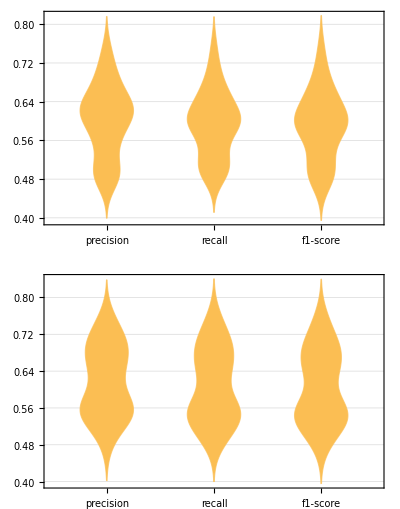

```mathematica
GraphicsGrid[{{DistributionChart[nnoise[[;;,;;]]ᵀ, ChartLabels->nnoise[[1,;;]],PlotTheme->"Detailed"]},{DistributionChart[noise[[;;,;;]]ᵀ, ChartLabels->nnoise[[1,;;]],PlotTheme->"Detailed"]}}]
```

```mathematica
WilksWTest[nnoise[[2;;,1]],noise[[2;;,1]]]
```

0.675168

```mathematica
With[
{x=nnoise[[2;;,1]],
y=noise[[2;;,1]]},
KolmogorovSmirnovTest[x,y,"PValueTable"]]
```

| P-Value
Kolmogorov-Smirnov | 0.592907

```mathematica
With[
{x=nnoise[[2;;,2]],
y=noise[[2;;,2]]},
KolmogorovSmirnovTest[x,y,"PValueTable"]]
```

| P-Value
Kolmogorov-Smirnov | 0.742543

```mathematica
With[
{x=nnoise[[2;;,3]],
y=noise[[2;;,3]]},
KolmogorovSmirnovTest[x,y,"PValueTable"]]
```

| P-Value
Kolmogorov-Smirnov | 0.822446

```mathematica
PairedHistogram[nnoise[[2;;,1]],noise[[2;;,1]], PlotTheme->"Detailed"]
```

-Graphics-